```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0]
```

ProbabilityDistribution[x^w ⅇ^(-(x Gamma[(2+w)/(1+w)])^(1+w)) (1+w) Gamma[(2+w)/(1+w)]^(1+w),{x,0,∞},Assumptions→w>0]

```mathematica
FitError[func_,list_,p_]:=Module[{tab1,nbin},
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}];
If[p==Null,
tab1=Table[(list[[i,2]]-func[list[[i,1]]])^2,{i,1,Length[list]}],
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}]
];
nbin=Length[tab1];
√(Total[tab1]/(nbin-1))
]
```

```mathematica
ResidualSum[func_,P_,param_]:=Module[{tab1,nbin,Ntot,dbin},
Ntot=Total[P[[All,2]]];
dbin=P[[2,1]]-P[[1,1]];
tab1=Table[(P[[i,2]]- func[P[[i,1]],param])^2,{i,1,Length[P]}];
Total[tab1]
]
```

```mathematica
ChiSqr[func_,hist_,p_]:=Module[{tab1,nbin,dbin,Ntot},
dbin=hist[[2,1]]-hist[[1,1]];
Ntot=Total[hist[[All,2]]];
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]],p])^2/(Ntot dbin  func[hist[[i,1]],p]),{i,1,Length[hist]}];
If[p== Null,
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]]])^2/(Ntot dbin  func[hist[[i,1]]]),{i,1,Length[hist]}]
];
nbin=Length[hist];
Total[tab1]
]
RedChiSqr[func_,hist_,p_,numfit_]:=ChiSqr[func,hist,p]/(Length[hist]-numfit);
```

```mathematica
SemiPoisson[s_]:=4 s Exp[-2 s]
```

```mathematica
porterthomas[x_]:=Exp[-x/2]/(√(2π x))
```

```mathematica
genpt[x_,ν_]:=(ν/2 x)^(ν/2-1)/Gamma[ν/2] ν/2 Exp[-ν/2 x]
```

```mathematica
GenPTDistribution=ProbabilityDistribution[genpt[x,ν],{x,0,∞},Assumptions->ν>0]
```

ProbabilityDistribution[(2^(-ν/2) ⅇ^(-(x ν)/2) ν (x ν)^(-1+ν/2))/Gamma[ν/2],{x,0,∞},Assumptions→ν>0]

```mathematica
genpt[x,1]
```

ⅇ^(-x/2)/(√(2 π) √x)

```mathematica
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.800","Table"];
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];*)
AWD=DeleteCases[DeleteCases[AllWidthData,AllWidthData[[1]]],{}];
WidthData[ic_,E1_,E2_]:=Select[AWD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
Select[AWD,(#1[[7]]>10^-1)&]*)
```

```mathematica
iens=1;icoup=2;
```

```mathematica
path1=StringJoin[{"~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.",ToString[iens*1000+icoup]}]
(*path1=StringJoin[{"~/Code/Nchannel/Square/CODES/fort.",ToString[iens*1000+icoup]}]*)
```

~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.1002

```mathematica
Data=DeleteCases[Import[path1,"Table"],{}];
```

```mathematica
iemax=Length[Data];iemin=1;
sigma=Table[{Data[[ie,2]],Data[[ie,10]]},{ie,iemin,iemax}];
lzclose=Table[{Data[[ie,2]], Log[Data[[ie,6]]]},{ie,iemin,iemax}];
alsqr=Table[{Data[[ie,2]],Data[[ie,5]]},{ie,iemin,iemax}];
albgsqr=Table[{Data[[ie,2]],Sin[Data[[ie,8]]]^2},{ie,iemin,iemax}];
phaseopi=Table[{Data[[ie,2]],Data[[ie,11]]},{ie,iemin,iemax}];
ltimedelay=Table[{Data[[ie,2]],Log[Data[[ie,12]]]},{ie,iemin,iemax}];
ascat = Table[{Data[[ie,2]],Data[[ie,4]]},{ie,iemin,iemax}];
abg=  Table[{Data[[ie,2]],Data[[ie,13]]},{ie,iemin,iemax}];
BSdet = Table[{Data[[ie,2]],Data[[ie,7]]},{ie,iemin,iemax}];
```

```mathematica
padding={{100,45},{80,0}};
imgsize={600,300};
yrange=All;
xrange={0,0.1};
aspctratio=Full;1/GoldenRatio;
pabg=ListPlot[abg,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a_bg/r_0"},LabelStyle->{16},PlotRange->{xrange,{-1000,1000}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
palsqr=ListPlot[{alsqr,albgsqr},Joined->True,PlotStyle->{{Black},{Red,Dotted}},Frame->True,FrameLabel->{"E/(ℏ^2/2μ r_0^2)",TraditionalForm[Sin[δ]^2]},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio,FrameTicks->{Automatic,Automatic}];
psigma=ListPlot[sigma,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","σ/r_0^2"},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
pstair=ListPlot[phaseopi,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","δ_0/π"},LabelStyle->{16},PlotRange->{xrange,All},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
plzc=ListPlot[lzclose,Joined->True,PlotStyle->{Red,Dashed},Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","log(Z_C)"},LabelStyle->{16},PlotRange->{xrange,{-7,18}},GridLines->Automatic,ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pltd=ListPlot[ltimedelay,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{(*"E/(ℏ^2/2μr_0^2)"*)None,TraditionalForm[Log[(τ ℏ)/(2μ Subscript[r, 0]^2)]]},LabelStyle->Large,PlotRange->{xrange,{-7,18}},GridLines->Automatic,FrameTicks->{Automatic,Automatic},ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pascat=ListPlot[ascat,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a/r_0"},LabelStyle->{16},PlotRange->{xrange,{-100,100}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
```

```mathematica
pbsdet=ListPlot[BSdet,Joined->True,PlotStyle->Black,Frame->True,LabelStyle->{16},PlotRange->{xrange,{-10^-100,10^-100}},AspectRatio->50/1000,ImageSize->{600,50},PlotRangeClipping->False,ImagePadding->{{100,45},{0,20}},FrameTicks->{None,None},ImageMargins->0,Axes->False,Epilog->{Text[Style["(d)",Bold,22],{-0.015,0}]}]
```

-Graphics-

```mathematica
AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.800","Table"],{}];
(*AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/fort.800","Table"],{}];*)
ResData[iens_,icoup_]:=Select[Select[AllResData,(#[[2]]==iens)&],(#[[3]]==icoup)&]
Resonances = ResData[iens,icoup];
NumRes=Length[Resonances];

ResLines=Table[ssbg  (EE-ER+q Γ/2)^2/((EE-ER)^2+(Γ/2)^2)/.{ssbg->Resonances[[ires,9]],ER->Resonances[[ires,5]],Γ->Resonances[[ires,7]],q->Resonances[[ires,8]]},{ires,1,NumRes}];
resplots=Table[Plot[Evaluate[ResLines[[ires]]],{EE,Resonances[[ires,5]]-2Resonances[[ires,7]],Resonances[[ires,5]]+2Resonances[[ires,7]]},PlotStyle->{Blue,Dashed},PlotRange->All,ImagePadding->padding,ImageSize->imgsize,AspectRatio->Full],{ires,1,NumRes}];
```

```mathematica
widthdata=Table[{Resonances[[ires,5]],Resonances[[ires,7]]},{ires,1,NumRes}];
qdata=Table[{Resonances[[ires,5]],Resonances[[ires,8]]},{ires,1,NumRes}];
```

```mathematica
pwidth=ListPlot[widthdata,PlotStyle->Black,Frame->True,LabelStyle->Medium,FrameLabel->{"E","Γ/(ℏ^2/2μr_0^2)"}];
```

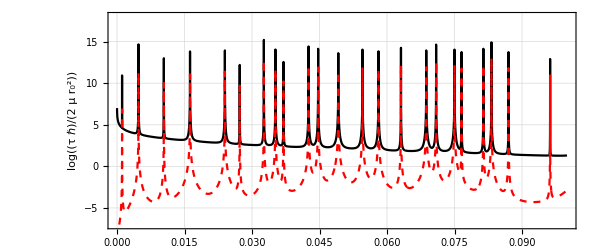

```mathematica
ptdlz=Show[{pltd,plzc},PlotRange->{xrange,{-7,18}},FrameLabel->{{TraditionalForm[Log[(τ ℏ)/(2μ Subscript[r, 0]^2)] ],TraditionalForm[Style[Log[Subscript[Z, C]],Red]]},{None,None}},PlotRangeClipping->False,Epilog->{Text[Style["(e)",Bold,22],{-.015,15.}]}]
```

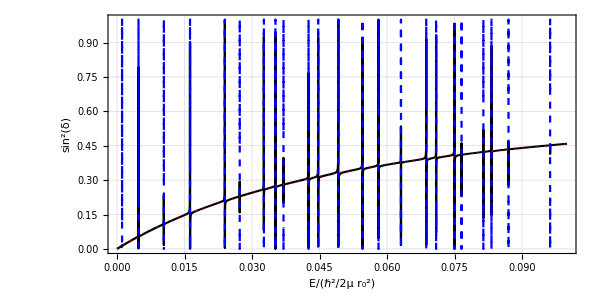

```mathematica
pfanolines = Show[{palsqr,resplots},PlotRange->{xrange,{0,1}},LabelStyle->Large,PlotRangeClipping->False,Epilog->{Text[Style["(f)",Bold,22],{-.015,0.9}]}]
```

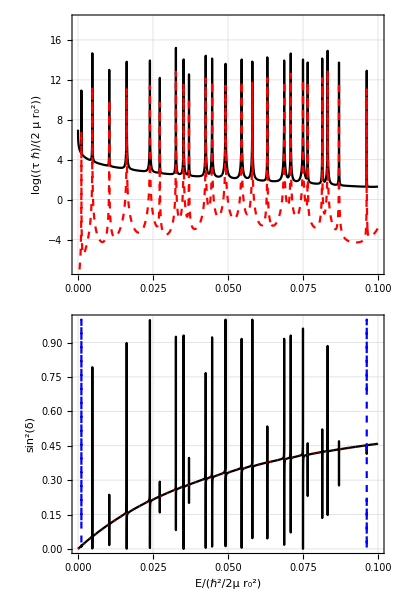

```mathematica
p1=Grid[{{pbsdet},{ptdlz},{pfanolines}},Spacings->0]
```

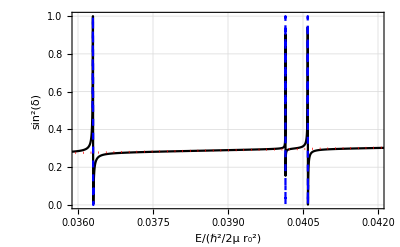

```mathematica
pfanofits=Show[pfanolines,PlotRange->{{0.036,0.042},All},ImagePadding->Automatic,ImageSize->Automatic,AspectRatio->1/GoldenRatio,PlotRangeClipping->True]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf",pfanofits]
```

~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-tridiag-chris-3chan-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-tridiag-chris-3chan-scat.pdf

### Statistical Data

```mathematica
AllResonanceData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];*)
```

```mathematica
ARD=DeleteCases[DeleteCases[AllResonanceData,AllResonanceData[[1]]],{}];
```

```mathematica
DataSelect[ic_,E1_,E2_]:=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
```

```mathematica
ic=1;
Emin=0.0;Emax=0.1;
DataSubset=DataSelect[ic,Emin,Emax];
```

```mathematica
Select[DataSubset,(#1[[7]]>10^-1)&]
```

{}

```mathematica
bins=Join[Table[x,{x,0.0,2.8,.1}],Table[x,{x,3.0,5,0.25}]]
(*bins=Table[x,{x,0.02,5,0.25}]*)
bfit=Table[0.5(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.9,3.125,3.375,3.625,3.875,4.125,4.375,4.625,4.875}

```mathematica
SummaryData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.700","Table"];
(*Sdat=Import["~/Code/Nchannel/Square/CODES/fort.700","Table"];*)
SD=DeleteCases[SummaryData,SummaryData[[1]]];
```

```mathematica
nw=Length[DataSubset]
```

3993

```mathematica
WidthArray=Table[DataSubset[[i,7]]/(√DataSubset[[i,5]]),{i,1,nw}];
```

```mathematica
Length[WidthArray]
```

3993

```mathematica
MeanWidth=Mean[WidthArray]
```

4.64732×10^-6

```mathematica
Median[WidthArray]
```

2.0749×10^-6

```mathematica
ScaledWidths=WidthArray/MeanWidth;
```

```mathematica
WidthBinCounts1=BinCounts[ScaledWidths,{bins}];
```

```mathematica
NormalizedWidthHistogram=Table[{bins[[i]],WidthBinCounts1[[i]]/nw/(bins[[i+1]]-bins[[i]])},{i,1,Length[bins]-1}];
```

```mathematica
nw
```

3993

```mathematica
FitWidthHistogram=Table[{bfit[[i]],WidthBinCounts1[[i]]/nw/(bins[[i+1]]-bins[[i]])},{i,1,Length[bfit]}]
```

{{0.05,2.49687},{0.15,0.991736},{0.25,0.643626},{0.35,0.608565},{0.45,0.528425},{0.55,0.425745},{0.65,0.360631},{0.75,0.318057},{0.85,0.298022},{0.95,0.26296},{1.05,0.225394},{1.15,0.215377},{1.25,0.190333},{1.35,0.187829},{1.45,0.180316},{1.55,0.122715},{1.65,0.117706},{1.75,0.135237},{1.85,0.137741},{1.95,0.110193},{2.05,0.107688},{2.15,0.0776359},{2.25,0.0826446},{2.35,0.0626096},{2.45,0.0550964},{2.55,0.0726271},{2.65,0.0400701},{2.75,0.0475833},{2.9,0.0413223},{3.125,0.0320561},{3.375,0.0420736},{3.625,0.0250438},{3.875,0.0240421},{4.125,0.0320561},{4.375,0.0180316},{4.625,0.0170298},{4.875,0.0130228}}

```mathematica
ν0=0.5;
ph=ListPlot[NormalizedWidthHistogram,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black];
(*w1nlm=FindFit[FitWidthHistogram,{genpt[γ,ν]},{{ν,1.0}},γ]*)
w1nlm=NonlinearModelFit[FitWidthHistogram,genpt[γ,ν],{ν},γ,Method->"LevenbergMarquardt"]
pgenpt=Plot[genpt[γ,ν/.w1nlm["BestFitParameters"]],{γ,0,5},PlotStyle->{Red},PlotRange->All];
```

NonlinearModelFit::nrlnum: The function value {-2.49687+genpt[0.05,1.],-0.991736+genpt[0.15,1.],-0.643626+genpt[0.25,1.],-0.608565+genpt[0.35,1.],-0.528425+genpt[0.45,1.],-0.425745+genpt[0.55,1.],-0.360631+genpt[0.65,1.],-0.318057+genpt[0.75,1.],«22»,-0.0420736+genpt[3.375,1.],-0.0250438+genpt[3.625,1.],-0.0240421+genpt[3.875,1.],-0.0320561+genpt[4.125,1.],-0.0180316+genpt[4.375,1.],-0.0170298+genpt[4.625,1.],-0.0130228+genpt[4.875,1.]} is not a list of real numbers with dimensions {37} at {ν} = {1.}.

NonlinearModelFit[{{0.05,2.49687},{0.15,0.991736},{0.25,0.643626},{0.35,0.608565},{0.45,0.528425},{0.55,0.425745},{0.65,0.360631},{0.75,0.318057},{0.85,0.298022},{0.95,0.26296},{1.05,0.225394},{1.15,0.215377},{1.25,0.190333},{1.35,0.187829},{1.45,0.180316},{1.55,0.122715},{1.65,0.117706},{1.75,0.135237},{1.85,0.137741},{1.95,0.110193},{2.05,0.107688},{2.15,0.0776359},{2.25,0.0826446},{2.35,0.0626096},{2.45,0.0550964},{2.55,0.0726271},{2.65,0.0400701},{2.75,0.0475833},{2.9,0.0413223},{3.125,0.0320561},{3.375,0.0420736},{3.625,0.0250438},{3.875,0.0240421},{4.125,0.0320561},{4.375,0.0180316},{4.625,0.0170298},{4.875,0.0130228}},genpt[γ,ν],{ν},γ,Method→LevenbergMarquardt]

General::ivar: 0.000102143 is not a valid variable.

ReplaceAll::reps: {NonlinearModelFit[{{0.05,2.49687},{0.15,0.991736},{0.25,0.643626},{0.35,0.608565},{0.45,0.528425},{0.55,0.425745},{0.65,0.360631},{0.75,0.318057},{0.85,0.298022},{0.95,0.26296},«18»,{2.9,0.0413223},{3.125,0.0320561},{3.375,0.0420736},{3.625,0.0250438},{3.875,0.0240421},{4.125,0.0320561},{4.375,0.0180316},{4.625,0.0170298},{4.875,0.0130228}},«3»,Method→L…dt][…]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.102143 is not a valid variable.

ReplaceAll::reps: {NonlinearModelFit[{{0.05,2.49687},{0.15,0.991736},{0.25,0.643626},{0.35,0.608565},{0.45,0.528425},{0.55,0.425745},{0.65,0.360631},{0.75,0.318057},{0.85,0.298022},{0.95,0.26296},«18»,{2.9,0.0413223},{3.125,0.0320561},{3.375,0.0420736},{3.625,0.0250438},{3.875,0.0240421},{4.125,0.0320561},{4.375,0.0180316},{4.625,0.0170298},{4.875,0.0130228}},«3»,Method→L…dt][…]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.204184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{0.05,2.49687},{0.15,0.991736},{0.25,0.643626},{0.35,0.608565},{0.45,0.528425},{0.55,0.425745},{0.65,0.360631},{0.75,0.318057},{0.85,0.298022},{0.95,0.26296},«18»,{2.9,0.0413223},{3.125,0.0320561},{3.375,0.0420736},{3.625,0.0250438},{3.875,0.0240421},{4.125,0.0320561},{4.375,0.0180316},{4.625,0.0170298},{4.875,0.0130228}},«3»,Method→L…dt][…]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
NumberForm[ν/.w1nlm["BestFitParameters"],{6,4}]
```

0.7703

```mathematica
√(2(D[ChiSqr[genpt,FitWidthHistogram,ν],{ν,2}]/.w1nlm["BestFitParameters"])^-1)
```

0.393511

```mathematica
w1nlm["ParameterErrors"]
```

{0.118715}

```mathematica
Total[w1nlm["FitResiduals"]^2]
```

0.467301

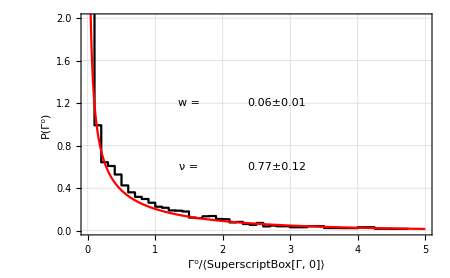

```mathematica
pporterthomas=Show[{ph,pgenpt},PlotRange->{0,2},Frame->True,GridLines->Automatic,FrameLabel->{"Γ^0/⟨SuperscriptBox[Γ, 0]⟩","P(Γ^0)"},LabelStyle->Large,Epilog->{
Text[Style["w = ",Large],{1.5,1.2}],
Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{3,2}],Large],{2.8,1.2}],
Text[Style["ν = ",Large],{1.5,0.6}],Text[Style[NumberForm[ν/.w1nlm["BestFitParameters"],{3,2}]±NumberForm[w1nlm["ParameterErrors"][[1]],{3,2}],Large],{2.8,0.6}]
(*,
Text[Style["SE_PT = ",Large],{2.6,0.4}],
Text[Style[NumberForm[FitError[porterthomas,wcfit,Null],{3,2}],Large],{3.7,0.4}],*)
(*Text[Style["SE_ad = ",Large],{2.0,0.2}],*)
}]
```

### Distribution for the time delay

```mathematica
Integrate[(1/2)^(M/2)Exp[-M /(2τ)]/(Gamma[M/2](M τ)^((M+4)/2))/.M->1,{τ,0,∞}]
```

1

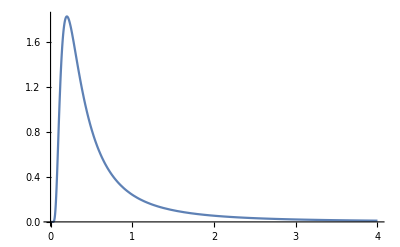

```mathematica
Plot[(1/2)^(M/2)Exp[-M /(2τ)]/(Gamma[M/2](M τ)^((M+4)/2))/.M->1,{τ,0,4},PlotRange->All]
```

```mathematica
ic=1;
WDtest=Select[AWD,(#1[[3]]==ic)&];
```

```mathematica
nw=Length[WDtest]
```

3996

```mathematica
tdarray=Table[4/WDtest[[i,7]],{i,1,nw}];
```

```mathematica
tdarray[[1]]
```

859328.

```mathematica
meantd=Mean[tdarray]
```

2.13676×10^8

```mathematica
Median[tdarray]
```

469528.

```mathematica
{Min[tdarray],Max[tdarray]}
```

{6622.52,3.02755×10^11}

```mathematica
dtb=0.1;tbins=Table[i,{i,0,4,dtb}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.}

```mathematica
tbinfit=Table[(tbins[[i]]+tbins[[i+1]])/2,{i,1,Length[tbins]-1}]
```

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95}

```mathematica
td1=BinCounts[tdarray/meantd,{tbins}]
```

{3684,94,37,30,22,8,16,11,7,3,2,2,0,3,6,2,4,1,2,3,5,4,2,2,1,0,0,0,0,0,4,1,1,2,2,0,0,0,0,0}

```mathematica
tdfit=Table[{tbinfit[[i]],td1[[i]]/nw/dtb},{i,1,Length[wcnorm]}];
```

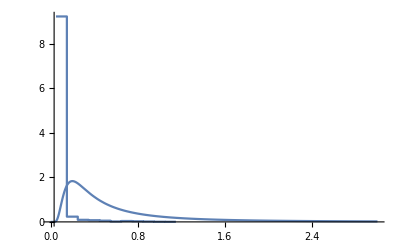

```mathematica
Show[{ListPlot[tdfit,InterpolationOrder->0,Joined->True,PlotRange->All],Plot[(1/2)^(M/2)Exp[-M /(2τ)]/(Gamma[M/2](M τ)^((M+4)/2))/.M->1,{τ,0,3}]},PlotRange->All]
```

Well... that doesn’t seem right at all.

### Zclose vs. width

```mathematica
Scaledgammazc[ic_,E1_,E2_]:=Module[{WidthData,i,nw},
WidthData=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];(*Select[AWDTrimmed,(#1[[3]]==ic )&];*)
nw=Length[WidthData];
Table[{WidthData[[i,7]]/√WidthData[[i,5]],WidthData[[i,6]]},{i,1,nw}]
]
```

```mathematica
gammazc[ic_,E1_,E2_]:=Module[{WidthData,i,nw},
WidthData=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];(*Select[AWDTrimmed,(#1[[3]]==ic )&];*)
nw=Length[WidthData];
Table[{WidthData[[i,7]],WidthData[[i,6]]},{i,1,nw}]
]
```

```mathematica
Length[ARD]
```

163128

```mathematica
ScaledAllgammazc=Table[{ARD[[i,7]]/√ARD[[i,5]],ARD[[i,6]]},{i,1,Length[ARD]}];
```

```mathematica
Allgammazc=Table[{ARD[[i,7]],ARD[[i,6]]},{i,1,Length[ARD]}];
```

```mathematica
punscaledgammazc=Show[{ListLogLogPlot[Allgammazc,PlotRange->{{10^-13,10^-3},{10^3,10^13}},Frame->True,LabelStyle->{12},PlotMarkers->{"●",1.0},PlotStyle->{Small,Black},FrameLabel->{TraditionalForm["Γ"/"ℏ^2/(2μ r_0^2)"],TraditionalForm[Subscript[Z, C]]},ImageSize->{500,500/1.6}],LogLogPlot[A (x)^b/.{A->2,b->-1},{x,10^-13,10^-0},PlotStyle->{Red,Dashed,Thin}]}];
```

```mathematica
pgammazc=Show[{ListLogLogPlot[ScaledAllgammazc,PlotRange->{{10^-13,10^-0},{10^3,10^13}},Frame->True,LabelStyle->{Large},PlotMarkers->{"●",1.0},PlotStyle->{Small,Black},FrameLabel->{TraditionalForm["Γ^0"/"√(ℏ^2)"],TraditionalForm[Subscript[Z, C]]},ImageSize->{700,700/1.6}],LogLogPlot[A (x)^b/.{A->2,b->-1},{x,10^-13,10^-0},PlotStyle->{Red,Dashed,Thin}]},Epilog->{Inset[punscaledgammazc,ImageScaled[{0.5,0.4}],ImageScaled[{0,0}],ImageScaled[{.48,.56}]]}];
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pgammazc.pdf",pgammazc]
```

~/Code/Nchannel/Square/CODES/plots/pgammazc.pdf

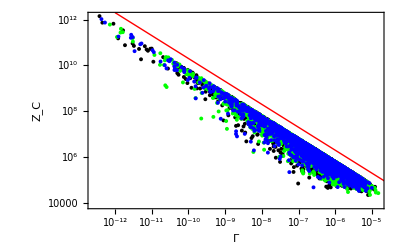

```mathematica
Show[{ListLogLogPlot[{gammazc[1,0.0,0.1],gammazc[10,0.0,0.1],gammazc[50,0.0,0.1]},Frame->True,LabelStyle->Large,PlotMarkers->{"●",4.0},PlotStyle->{{Small,Black},{Small,Green},{Small,Blue}},FrameLabel->{TraditionalForm[Γ],TraditionalForm[Subscript[Z, C]]}],
(*ListLogLogPlot[gammazc[2],Frame->True,LabelStyle->Large,PlotMarkers->{"●",2.0},PlotStyle->{Small,Blue},FrameLabel->{TraditionalForm[Γ],TraditionalForm[Subscript[Z, C]]}],*)
LogLogPlot[A (x)^b/.{A->2,b->-1},{x,10^-12,10^1},PlotStyle->{Red,Thin}]}]
```

```mathematica
Spoles[ic_,E1_,E2_]:=Module[{WidthData,i,nw},
WidthData=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];(*Select[AWD,(#1[[3]]==ic )&];*)
nw=Length[WidthData];
Table[{WidthData[[i,5]],WidthData[[i,7]]/(√WidthData[[i,5]])},{i,1,nw}]
]
```

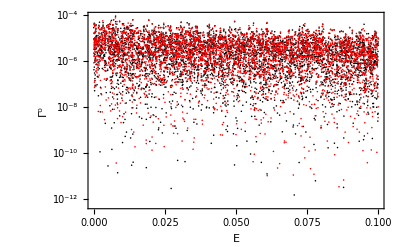

```mathematica
Dom={0.0,0.1};ListLogPlot[{Spoles[1,Dom[[1]],Dom[[2]]],Spoles[2,Dom[[1]],Dom[[2]]]},Frame->True,LabelStyle->Large,PlotStyle->{{Black,Small},{Red,Small}},FrameLabel->{TraditionalForm["E"],TraditionalForm["Γ^0"]},PlotRange->{Dom,All}]
```

### Level Spacings with Mathematica

```mathematica
genpt[x_,ν_]:=(ν/2 x)^(ν/2-1)/Gamma[ν/2] ν/2 Exp[-ν/2 x]
```

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0]
```

ProbabilityDistribution[x^w ⅇ^(-(x Gamma[(2+w)/(1+w)])^(1+w)) (1+w) Gamma[(2+w)/(1+w)]^(1+w),{x,0,∞},Assumptions→w>0]

```mathematica
SemiPoisson[s_]:=4 s Exp[-2 s]
```

```mathematica
porterthomas[x_]:=Exp[-x/2]/(√(2π x))
```

```mathematica
GenPTDistribution=ProbabilityDistribution[genpt[x,ν],{x,0,∞},Assumptions->ν>0]
```

ProbabilityDistribution[(2^(-ν/2) ⅇ^(-(x ν)/2) ν (x ν)^(-1+ν/2))/Gamma[ν/2],{x,0,∞},Assumptions→ν>0]

```mathematica
AllResonanceData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];*)
ARD=DeleteCases[DeleteCases[AllResonanceData,AllResonanceData[[1]]],{}];
DataSelect[ic_,E1_,E2_]:=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
```

```mathematica
LevelSpacings[ic_,nens_,ARD_]:=Module[{datatemp,nr,ls,iens},
datatemp=Table[Select[ARD,(#1[[3]]==ic && #1[[2]]==iens)&],{iens,1,nens}];
nr=Table[Length[datatemp[[iens]]],{iens,1,nens}];
ls=Table[Table[datatemp[[iens,i+1,5]]-datatemp[[iens,i,5]],{i,1,nr[[iens]]-1}],{iens,1,nens}];
ls=Flatten[ls];
ls = ls/Mean[ls]
]
```

```mathematica
(*ls=Table[LevelSpacings[ic,100,ARD],{ic,1,50}];*)
```

```mathematica
(*Export["~/Code/Nchannel/Square/CODES/plots/linespacings.dat",ls]*)
```

~/Code/Nchannel/Square/CODES/plots/linespacings.dat

```mathematica
ls=Import["~/Code/Nchannel/Square/CODES/plots/linespacings.dat","Table"];
```

```mathematica
r1=Table[FindDistributionParameters[ls[[ic]],BrodyDistribution],{ic,1,50}]
```

{{w→0.0499654},{w→0.12031},{w→0.192342},{w→0.255456},{w→0.312029},{w→0.367889},{w→0.416437},{w→0.461146},{w→0.507934},{w→0.551645},{w→0.58677},{w→0.627763},{w→0.665902},{w→0.69149},{w→0.714167},{w→0.735682},{w→0.748762},{w→0.769472},{w→0.791131},{w→0.803094},{w→0.818632},{w→0.835699},{w→0.847166},{w→0.860136},{w→0.870283},{w→0.879756},{w→0.890347},{w→0.89366},{w→0.90458},{w→0.899762},{w→0.905678},{w→0.90589},{w→0.897901},{w→0.894926},{w→0.890297},{w→0.88223},{w→0.883776},{w→0.883657},{w→0.885711},{w→0.893603},{w→0.900819},{w→0.911948},{w→0.920108},{w→0.925237},{w→0.931174},{w→0.939581},{w→0.947278},{w→0.951065},{w→0.950262},{w→0.955276}}

```mathematica
NewBrodyBC=Table[BinCounts[ls[[ic]],{bins}],{ic,1,50}];
NormalizedBrodyBC=Table[Table[NewBrodyBC[[ic,i]]/Total[NewBrodyBC[[ic]]]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}],{ic,1,50}];
RawBrodyHistogram=Table[Table[{bins[[i]],NewBrodyBC[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,50}];
RawFitBrodyHistogram=Table[Table[{bfit[[i]],NewBrodyBC[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,50}];
```

```mathematica
NewBrodyPDist=Table[Table[{bfit[[i]],NormalizedBrodyBC[[ic,i]]},{i,1,Length[bfit]}],{ic,1,50}];
```

```mathematica
BrodyFitNLM=Table[NonlinearModelFit[NewBrodyPDist[[ic]],PBrody[z,w],{w},z,PrecisionGoal->0.001,Method->Automatic,ConfidenceLevel->0.9],{ic,1,50}];
```

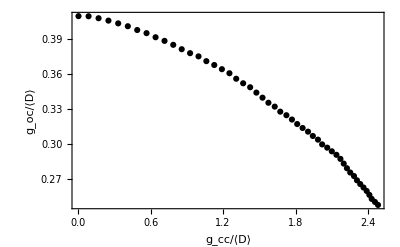

```mathematica
gocdata=Table[{SD[[i,5]],SD[[i,4]]},{i,1,Length[SD]}];
pgocplot=ListPlot[gocdata,PlotStyle->Black,Frame->True,FrameLabel->{"g_cc/⟨D⟩","g_oc/⟨D⟩"},LabelStyle->{12}]
```

```mathematica
brodydata=Table[{SD[[ic,5]],w/.BrodyFitNLM[[ic]]["BestFitParameters"]},{ic,1,Length[SD]}];
brodyfiterror=Table[BrodyFitNLM[[ic]]["ParameterErrors"][[1]],{ic,1,Length[SD]}];
brodydatap=Table[{brodydata[[ic,1]],brodydata[[ic,2]]+brodyfiterror[[ic]]},{ic,1,Length[SD]}];
brodydatam=Table[{brodydata[[ic,1]],brodydata[[ic,2]]-brodyfiterror[[ic]]},{ic,1,Length[SD]}];
```

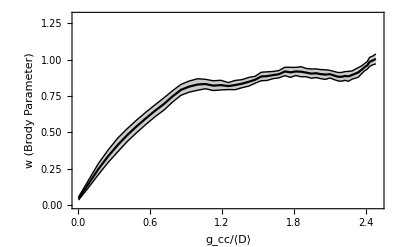

```mathematica
pbrody1=ListPlot[{brodydatam,brodydata,brodydatap},Frame->True,PlotStyle->{{Black,Thin},{Black},{Black,Thin}},Filling->{1->{3}},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","w (Brody Parameter)"},GridLines->None,PlotRange->{{0,2.5},{0,1.3}},Epilog->{Inset[pgocplot,{1.6,.37},{Automatic,Automatic},{1.4,0.7}]}]
```

```mathematica
DataArray=Table[DataSelect[ic,0,0.1],{ic,1,Length[SD]}];
```

```mathematica
nw=Table[Length[DataArray[[ic]]],{ic,1,Length[SD]}]
```

{3993,3994,3978,3964,3947,3923,3898,3872,3846,3815,3790,3764,3728,3683,3656,3612,3582,3547,3514,3476,3437,3402,3373,3311,3278,3249,3214,3174,3141,3108,3057,3026,2985,2948,2917,2884,2856,2820,2797,2771,2735,2694,2661,2632,2588,2552,2530,2504,2470,2432}

```mathematica
WidthArrayTemp=Table[Table[(DataArray[[ic]][[i,7]])/(√(DataArray[[ic]][[i,5]])),{i,1,nw[[ic]]}],{ic,1,Length[SD]}];
```

```mathematica
MeanWidth=Table[Mean[WidthArrayTemp[[ic]]],{ic,1,Length[SD]}];
```

```mathematica
ScaledWidthArray=Table[WidthArrayTemp[[ic]]/MeanWidth[[ic]],{ic,1,Length[SD]}];
```

```mathematica
WidthCountsTemp=Table[BinCounts[ScaledWidthArray[[ic]],{bins}],{ic,1,Length[SD]}];
```

```mathematica
WidthCountsTemp[[1]]
```

{997,396,257,243,211,170,144,127,119,105,90,86,76,75,72,49,47,54,55,44,43,31,33,25,22,29,16,19,33,32,42,25,24,32,18,17,13}

```mathematica
RawFitWidthHistograms=Table[Table[{(bins[[i]]+bins[[i+1]])/2,WidthCountsTemp[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,Length[SD]}];
RawWidthHistograms=Table[Table[{(bins[[i]]),WidthCountsTemp[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,Length[SD]}];
```

```mathematica
NormalizedWidthHistTemp=Table[Table[{bins[[i]],WidthCountsTemp[[ic,i]]/nw[[ic]]/(bins[[i+1]]-bins[[i]])},{i,1,Length[bins]-1}],{ic,1,Length[SD]}];
```

```mathematica
WidthFitHist=Table[Table[{bfit[[i]],NormalizedWidthHistTemp[[ic,i,2]]},{i,1,Length[bfit]}],{ic,1,Length[SD]}];
```

```mathematica
Widthnlm=Table[NonlinearModelFit[WidthFitHist[[ic]],{genpt[γ,ν]},{{ν,1.0}},γ,Method->Automatic],{ic,1,Length[SD]}];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

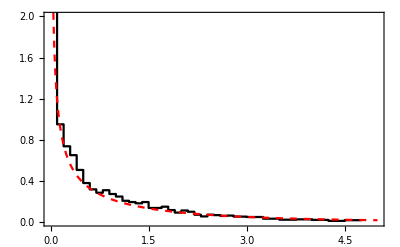

```mathematica
ic=50;ppt1=Show[ListPlot[NormalizedWidthHistTemp[[ic]],Joined->True,InterpolationOrder->0,PlotRange->{0,3},Frame->True,PlotStyle->Black,LabelStyle->Large],Plot[genpt[γ,ν/.Widthnlm[[ic]]["BestFitParameters"]],{γ,0,5},PlotRange->{0,3},PlotStyle->{Red,Dashed}],PlotRange->{0,2}]
```

```mathematica
√(Widthnlm[[1]]["CovarianceMatrix"])
```

{{0.118715}}

```mathematica
Widthnlm[[1]]["ParameterErrors"]
```

{0.118715}

```mathematica
SD[[1]]
```

{1,1,0.0024445,0.40909,0.0040909,0.00035698,0.055357,0.0084496}

```mathematica
histnufittable=Table[{SD[[ic,5]],ν/.FindDistributionParameters[ScaledWidthArray[[ic]],GenPTDistribution,ParameterEstimator->"MaximumLikelihood"]},{ic,1,Length[SD]}]
```

{{0.0040909,0.991874},{0.087476,0.989675},{0.17015,0.992211},{0.25192,0.991151},{0.3326,0.976445},{0.41224,0.985971},{0.48993,0.977755},{0.56708,0.977612},{0.6418,0.976767},{0.71583,0.97778},{0.78805,0.956439},{0.85805,0.954175},{0.92742,0.954861},{0.99716,0.946357},{1.0619,0.94584},{1.1274,0.945109},{1.1906,0.928485},{1.2529,0.94847},{1.309,0.966002},{1.3665,0.976111},{1.4244,0.98236},{1.4759,0.970136},{1.5267,0.961888},{1.5756,0.959606},{1.6278,0.965186},{1.6735,0.949615},{1.7243,0.936411},{1.7701,0.9601},{1.8136,0.969156},{1.8584,0.978387},{1.9032,0.973365},{1.9432,0.966214},{1.9854,0.967855},{2.02,0.979068},{2.0619,0.963183},{2.1001,0.985502},{2.1382,0.977157},{2.1713,0.973961},{2.1987,0.988134},{2.2251,1.0005},{2.2524,0.989304},{2.2835,0.988806},{2.308,0.988096},{2.3351,0.995932},{2.3625,0.985505},{2.3888,0.985079},{2.4108,0.995491},{2.4302,1.00019},{2.4568,0.992793},{2.4822,0.986342}}

```mathematica
ℋ=DistributionFitTest[ScaledWidthArray[[1]],GenPTDistribution/.FindDistributionParameters[ScaledWidthArray[[1]],GenPTDistribution,ParameterEstimator->"MaximumLikelihood"],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
ℋ[{"TestDataTable",All}]
```

| Statistic | P-Value
Anderson-Darling | 1.22646 | 0.257669
Cramér-von Mises | 0.168091 | 0.338867
Kolmogorov-Smirnov | 0.014944 | 0.331251
Kuiper | 0.0217509 | 0.278201
Pearson χ^2 | 73.879 | 0.0455641
Watson U^2 | 0.125148 | 0.169042

```mathematica
S=SmoothKernelDistribution[ScaledWidthArray[[1]]]
```

DataDistribution[…]

```mathematica
f[ν]=LogLikelihood[GenPTDistribution,ScaledWidthArray[[1]]];
```

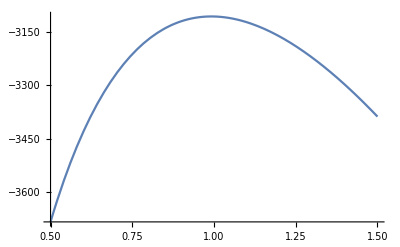

```mathematica
Plot[f[ν],{ν,.5,1.5}]
```

```mathematica
Plot[
```

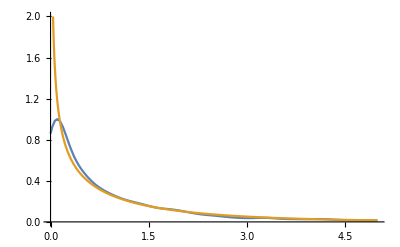

```mathematica
Plot[{PDF[S,x],genpt[x,1]},{x,0,5},PlotRange->{0,2}]
```

```mathematica
nudata=Table[{SD[[ic,5]],ν/.Widthnlm[[ic]]["BestFitParameters"]},{ic,1,Length[SD]}];
```

```mathematica
nuerror=Table[Widthnlm[[ic]]["ParameterErrors"][[1]],{ic,1,Length[SD]}]
```

{0.0564801,0.0510222,0.0510629,0.0527028,0.0577618,0.0521182,0.0522006,0.0519469,0.0522291,0.0545665,0.0637773,0.060159,0.0590108,0.0609811,0.0692598,0.0721348,0.0754437,0.0676558,0.0585006,0.0524436,0.0513314,0.0489254,0.051458,0.0549891,0.0549162,0.0680777,0.0709004,0.07068,0.0657896,0.0638057,0.0605523,0.0562776,0.0609933,0.0596492,0.0593683,0.0609723,0.0611472,0.0537792,0.0540526,0.0516334,0.0548783,0.0581931,0.0602922,0.0578188,0.0569751,0.0572042,0.0611408,0.0587866,0.0569944,0.0547015}

```mathematica
nudatap=Table[{nudata[[ic,1]],nudata[[ic,2]]+nuerror[[ic]]},{ic,1,Length[nudata]}];
nudatam=Table[{nudata[[ic,1]],nudata[[ic,2]]-nuerror[[ic]]},{ic,1,Length[nudata]}];
```

```mathematica
nuplot1=ListPlot[{nudatam,nudata,nudatap},Frame->True,LabelStyle->Large,PlotStyle->{{Red,Thin},{Red},{Red,Thin}},Joined->True,PlotRange->{0,1.4},Joined->True,Filling->{1->{3}}];
```

```mathematica
l1=ImageCrop[Graphics[{Red,Thick,Line[{{0,0},{.1,0}}]}]]
l2=ImageCrop[Graphics[{Black,Thick,Line[{{0,0},{.1,0}}]}]]
```

-Graphics-

-Graphics-

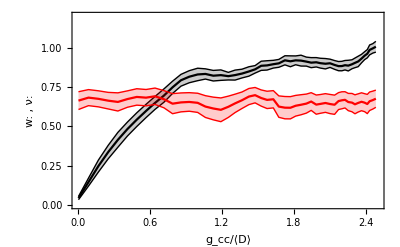

```mathematica
pbrody=Show[{pbrody1,nuplot1(*,ListPlot[histnufittable,PlotStyle->Red]*)},PlotRange->{{0,2.5},{0,1.2}},FrameLabel->{"g_cc/⟨D⟩","w: , ν: "}]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pbrody.pdf",pbrody]
```

~/Code/Nchannel/Square/CODES/plots/pbrody.pdf

```mathematica
yrange={0,1.15};
```

```mathematica
impad1={{80,10},{95,5}};imagewidth=400;options1={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->{imagewidth,300},ImagePadding->impad1,FrameTicksStyle->{None,Automatic},AspectRatio->Full};
```

```mathematica
NormalizedBrodyDist=Table[Table[{bins[[i]],NormalizedBrodyBC[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,50}];
```

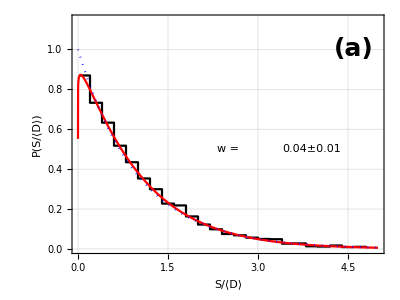

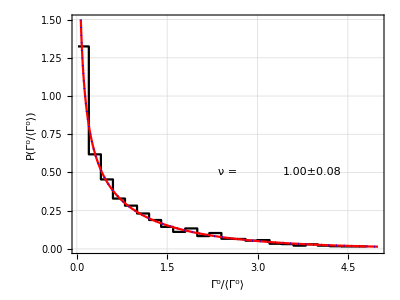

```mathematica
ic=1;
ppoisson=Show[ListPlot[NormalizedBrodyDist[[ic]],FrameLabel->{"S/⟨D⟩","P(S/⟨D⟩)"},options1,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[{PBrody[x,brodydata[[ic,2]]],PBrody[x,0.00000001]},{x,0,5},PlotStyle->{{Red},{Blue,Dotted}}],options1,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[brodydata[[ic,2]],{2,2}]±NumberForm[brodyfiterror[[ic]],{2,2}],Large],{3.9,0.5}],Text[Style["(a)",25,Bold],{4.6,1}]},PlotRangeClipping->False]

ppt1=Show[ListPlot[NormalizedWidthHistTemp[[ic]],FrameLabel->{"Γ^0/⟨Γ^0⟩","P(Γ^0/⟨Γ^0⟩)"},PlotRange->{0,5},options1,
Joined->True,InterpolationOrder->0,PlotRange->{0,1.5},Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic],Plot[{genpt[γ,ν/.Widthnlm[[ic]]["BestFitParameters"]],genpt[γ,1.0]},{γ,0,5},PlotRange->{0,1.5},PlotStyle->{{Red},{Blue,Dotted}}],PlotRange->{0,1.5},
ImageSize->{imagewidth,300},
ImagePadding->impad1,
AspectRatio->Full,
Epilog->{Text[Style["ν = ",Large],{2.5,0.5}],Text[Style[NumberForm[ν/.Widthnlm[[ic]]["BestFitParameters"],{2,2}]±NumberForm[Widthnlm[[ic]]["ParameterErrors"][[1]],{2,2}],Large],{3.9,0.5}](*,Text[Style["(b)",25,Bold],{4.6,1.35}]*)}
]
```

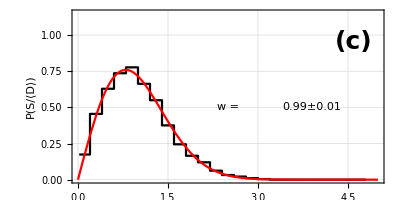

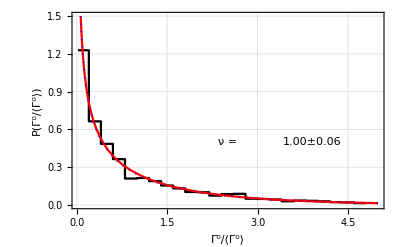

```mathematica
ic=50;
impad2={{80,10},{7,2}};
options={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->{imagewidth,200},ImagePadding->impad2,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},AspectRatio->Full};
pwigner=Show[ListPlot[NormalizedBrodyDist[[ic]],options1,InterpolationOrder->0,FrameLabel->{None,"P(S/⟨D⟩)"},Joined->True,PlotStyle->Black],Plot[PBrody[x,brodydata[[ic,2]]],{x,0,5},PlotStyle->Red],options,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[brodydata[[ic,2]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}],Text[Style["(c)",25,Bold],{4.6,.95}]},PlotRangeClipping->False]
ppt50=Show[ListPlot[NormalizedWidthHistTemp[[ic]],FrameLabel->{"Γ^0/⟨Γ^0⟩","P(Γ^0/⟨Γ^0⟩)"},PlotRange->{0,5},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->{400,400/1.6},
Joined->True,InterpolationOrder->0,PlotRange->{0,1.5},Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic],Plot[{genpt[γ,ν/.Widthnlm[[ic]]["BestFitParameters"]],genpt[γ,1.0]},{γ,0,5},PlotRange->{0,1.5},PlotStyle->{{Red},{Blue,Dotted}}],PlotRange->{0,1.5},
(*FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},*)
Epilog->{Text[Style["ν = ",Large],{2.5,0.5}],Text[Style[NumberForm[ν/.Widthnlm[[ic]]["BestFitParameters"],{2,2}]±NumberForm[Widthnlm[[ic]]["ParameterErrors"][[1]],{2,2}],Large],{3.9,0.5}](*,*)(*Text[Style["(b)",25,Bold],{4.6,1.35}]*)}
]
```

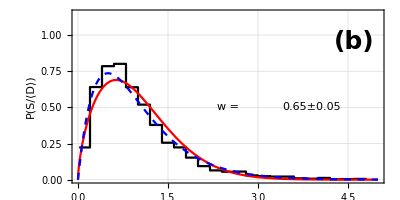

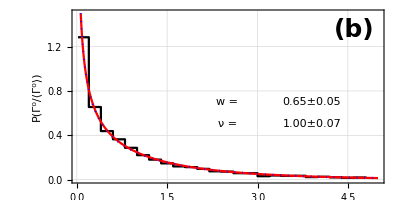

```mathematica
ic=9;
pmiddle=Show[{ListPlot[NormalizedBrodyDist[[ic]],options,InterpolationOrder->0,Joined->True,PlotStyle->Black,FrameLabel->{None,"P(S/⟨D⟩)"}],Plot[PBrody[x,brodydata[[ic,2]]],{x,0,5},PlotStyle->Red],Plot[4 s Exp[-2 s],{s,0,5},PlotStyle->{Blue,Dashed}]},options,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[brodydata[[ic,2]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}],(*Text[Style["SE_SP = ",Large],{3.0,0.3}],Text[Style[NumberForm[FitError[SemiPoisson,pfit,Null],{2,2}],Large],{3.9,0.3}]*),
Text[Style["(b)",25,Bold],{4.6,.95}]},PlotRangeClipping->False]
pptmid=Show[ListPlot[NormalizedWidthHistTemp[[ic]],FrameLabel->{None,"P(Γ^0/⟨Γ^0⟩)"},PlotRange->{0,5},options,
Joined->True,InterpolationOrder->0,Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic],Plot[{genpt[γ,ν/.Widthnlm[[ic]]["BestFitParameters"]],genpt[γ,1.0]},{γ,0,5},PlotRange->{0,1.5},PlotStyle->{{Red},{Blue,Dotted}}],PlotRange->{0,1.5},FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["w = ",Large],{2.5,0.7}],Text[Style[NumberForm[brodydata[[ic,2]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.7}],Text[Style["ν = ",Large],{2.5,0.5}],Text[Style[NumberForm[ν/.Widthnlm[[ic]]["BestFitParameters"],{2,2}]±NumberForm[Widthnlm[[ic]]["ParameterErrors"][[1]],{2,2}],Large],{3.9,0.5}],Text[Style["(b)",25,Bold],{4.6,1.35}]}]
```

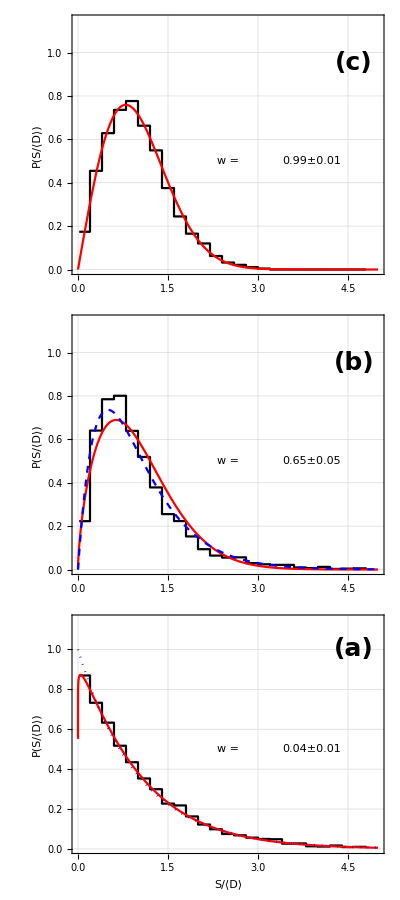

```mathematica
pstats=Grid[{{pwigner},{pmiddle},{ppoisson}},Spacings->0]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pstats.pdf",pstats]
```

~/Code/Nchannel/Square/CODES/plots/pstats.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pporterthomas.pdf",ppt50]
```

~/Code/Nchannel/Square/CODES/plots/pporterthomas.pdf

```mathematica
DataArray=Table[DataSelect[ic,0,0.1],{ic,1,Length[SD]}];
nw=Table[Length[DataArray[[ic]]],{ic,1,Length[SD]}]
```

```mathematica
bins=Join[Table[x,{x,0.0,2.0,.1}],Table[x,{x,2.1,5,0.4}]]
(*bins=Table[x,{x,0.02,5,0.25}]*)
bfit=Table[0.5(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.5,2.9,3.3,3.7,4.1,4.5,4.9}

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.3,2.7,3.1,3.5,3.9,4.3,4.7}

```mathematica
WidthArrayTemp=Table[Table[(DataArray[[ic]][[i,7]])/(√(DataArray[[ic]][[i,5]])),{i,1,nw[[ic]]}],{ic,1,Length[SD]}];
MeanWidth=Table[Mean[WidthArrayTemp[[ic]]],{ic,1,Length[SD]}];
ScaledWidthArray=Table[WidthArrayTemp[[ic]]/MeanWidth[[ic]],{ic,1,Length[SD]}];
WidthCountsTemp=Table[BinCounts[ScaledWidthArray[[ic]],{bins}],{ic,1,Length[SD]}];
```

```mathematica
WidthHistograms=Table[Table[{(bins[[i]]+bins[[i+1]])/2,WidthCountsTemp[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,Length[SD]}];
```

```mathematica
chi2widths=Table[
{SD[[ic,5]],RedChiSqr[genpt,RawFitWidthHistograms[[ic]],ν/.Widthnlm[[ic]]["BestFitParameters"],1]},{ic,1,50}]
```

{{0.0040909,12.0514},{0.087476,10.951},{0.17015,12.2022},{0.25192,12.8425},{0.3326,12.1937},{0.41224,11.7704},{0.48993,12.706},{0.56708,13.059},{0.6418,13.5621},{0.71583,13.3801},{0.78805,12.8347},{0.85805,13.1479},{0.92742,14.7265},{0.99716,14.5552},{1.0619,13.2493},{1.1274,13.6707},{1.1906,14.2405},{1.2529,14.3671},{1.309,14.0247},{1.3665,12.6846},{1.4244,12.5992},{1.4759,12.1594},{1.5267,12.1756},{1.5756,11.6122},{1.6278,11.6012},{1.6735,10.6258},{1.7243,10.0684},{1.7701,10.1676},{1.8136,10.2041},{1.8584,10.377},{1.9032,9.73103},{1.9432,9.6661},{1.9854,10.1535},{2.02,9.82707},{2.0619,10.2445},{2.1001,9.82937},{2.1382,9.66295},{2.1713,9.21141},{2.1987,7.60233},{2.2251,7.92225},{2.2524,8.04887},{2.2835,8.40189},{2.308,8.2251},{2.3351,8.14376},{2.3625,7.90444},{2.3888,7.26126},{2.4108,7.13677},{2.4302,6.42239},{2.4568,6.61836},{2.4822,6.82357}}

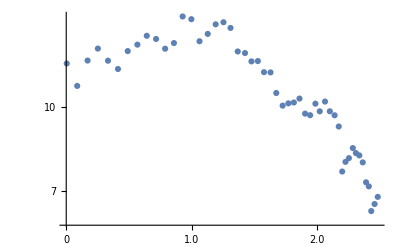

```mathematica
ListLogPlot[chi2widths,Ticks->All]
```

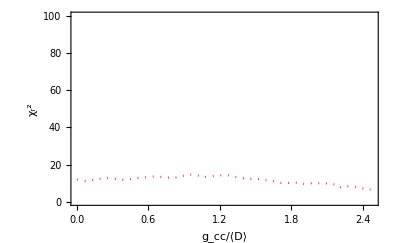

```mathematica
pwidthptchisqr=ListPlot[chi2widths,PlotRange->{0.1,100},FrameTicks->{{All,None},{All,None}},Frame->True,PlotStyle->{Red,Dotted},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ_r^2"}]
(*pwidthptchisqr=ListPlot[Table[
{SD[[ic,5]](*w/.nlmbrody[[ic]]["BestFitParameters"]*),Total[(Widthnlm[[ic]]["FitResiduals"])^2]},{ic,1,50}],Frame->True,PlotStyle->{Red,Dotted},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ^2"},GridLines->None,Axes->False]*)
```

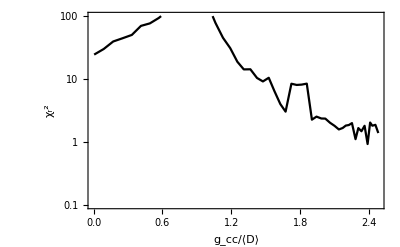

```mathematica
pbrodychisqr=ListLogPlot[Table[
{SD[[ic,5]],RedChiSqr[PBrody,RawFitBrodyHistogram[[ic]],w/.BrodyFitNLM[[ic]]["BestFitParameters"],1]},{ic,1,50}],PlotRange->{0.1,100},FrameTicks->{{All,None},{All,None}},Frame->True,PlotStyle->Black,Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ_r^2"},GridLines->None,PlotRange->All]
(*pbrodychisqr=ListPlot[Table[
{SD[[ic,5]],Total[(nlmbrody[[ic]]["FitResiduals"])^2]},{ic,1,50}],Frame->True,PlotStyle->Black,Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ^2"},GridLines->None,PlotRange->All]*)
```

```mathematica
pspchisqr=ListLogPlot[Table[
{SD[[ic,5]],RedChiSqr[SemiPoisson,RawFitBrodyHistogram[[ic]],Null]},{ic,1,50}],Frame->True,PlotStyle->{Black,Dashed},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ^2"},GridLines->None,FrameTicks->{{All,None},{All,None}}]
```

-Graphics-

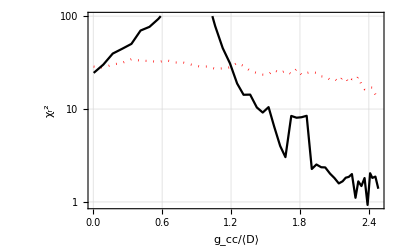

```mathematica
pchisqr=Show[{pwidthptchisqr,pspchisqr,pbrodychisqr},PlotRange->All,GridLines->Automatic]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/ChiSqrPlot.pdf",pchisqr]
```

~/Code/Nchannel/Square/CODES/plots/ChiSqrPlot.pdf

```mathematica
Length[ARD]
```

163128

### Width data...

```mathematica
avgwidths=Table[{SD[[i,5]],SD[[i,6]]SD[[i,3]]},{i,1,Length[SD]}];
```

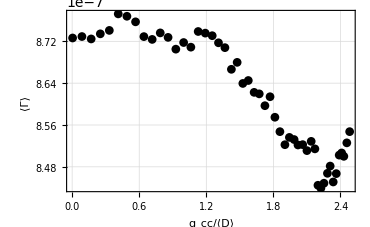

```mathematica
ListPlot[avgwidths,Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic,PlotRange->All,Joined->False,PlotMarkers->Automatic,FrameLabel->{"g_cc/⟨D⟩","⟨Γ⟩"}]
```

```mathematica
avgwidths2=Table[{SD[[i,4]],SD[[i,6]]},{i,1,Length[SD]}];
```

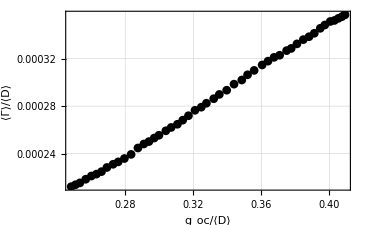

```mathematica
ListPlot[avgwidths2,Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic,PlotRange->All,Joined->False,PlotMarkers->Automatic,FrameLabel->{"g_oc/⟨D⟩","⟨Γ⟩/⟨D⟩"}]
```

```mathematica
MeanW[ic_,E1_,E2_]:=Module[{WidthData,i,nw,w},
WidthData=DataSelect[ic,E1,E2];
nw=Length[WidthData];
w=Table[WidthData[[i,7]],{i,1,nw}];
{Mean[w],StandardDeviation[w],nw}
]
```

```mathematica
ic=10;
mw=MeanW[1,0,0.1];mw[[2]]/√mw[[3]]
```

1.98227×10^-8

```mathematica
t=MeanW[1,Emin,Emax]
```

{8.72275×10^-7,1.2526×10^-6,3993}

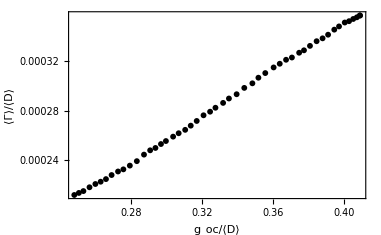

```mathematica
Emin=0.0;Emax=0.1;w1=ErrorListPlot[Table[t=MeanW[ic,Emin,Emax];{{SD[[ic,4]],t[[1]]/SD[[ic,3]] },ErrorBar[(t[[2]]/√t[[3]])]},{ic,1,Length[SD]}],Joined->False,PlotStyle->Black,Frame->True,PlotRange->All,FrameLabel->{"g_oc/⟨D⟩","⟨Γ⟩/⟨D⟩"},LabelStyle->{Large}]
```

### Number variance of resonances

```mathematica
ic=50;iens=2;
DataKeep=Select[ARD,(#1[[3]]==ic && #1[[2]]==iens)&];
nw=Length[DataKeep]
```

24

```mathematica
rpos=Table[DataKeep[[i,5]],{i,1,nw}]
```

{0.0025048,0.0044937,0.013442,0.018354,0.01974,0.022861,0.027451,0.028615,0.031919,0.038395,0.040348,0.049826,0.053422,0.057946,0.060167,0.065107,0.070435,0.074552,0.078588,0.082017,0.08484,0.089559,0.092336,0.094748}

```mathematica
tab1=Table[{DataKeep[[i,5]],i-1},{i,1,nw}];
f1=Interpolation[tab1,InterpolationOrder->0]
```

InterpolatingFunction[{{0.0025048, 0.094748}}, <>]

```mathematica
rpos
```

{0.0025048,0.0044937,0.013442,0.018354,0.01974,0.022861,0.027451,0.028615,0.031919,0.038395,0.040348,0.049826,0.053422,0.057946,0.060167,0.065107,0.070435,0.074552,0.078588,0.082017,0.08484,0.089559,0.092336,0.094748}

0.1

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

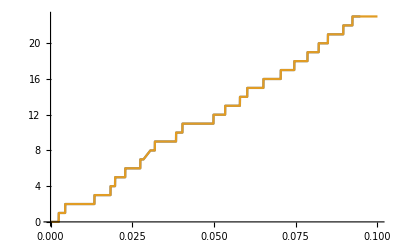

```mathematica
Emin=0.0;Emax=0.1
Plot[{(i=FirstPosition[rpos,u_/;u>EE,0][[1]];i-1),f1[EE]},{EE,Emin,Emax}]
```

InterpolatingFunction::dmval: Input value {1.01111×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

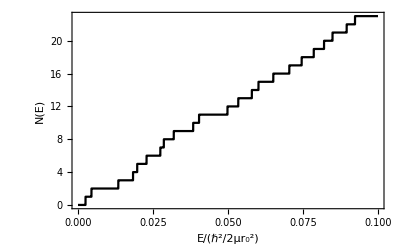

```mathematica
Plot[f1[EE],{EE,Emin,Emax},Frame->True,LabelStyle->Large,PlotStyle->Black,FrameLabel->{"E/(ℏ^2/2μr_0^2)","N(E)"},PlotPoints->100]
```

```mathematica
DataKeep=Select[ARD,(#1[[3]]==ic && #1[[2]]==iens)&];
```

```mathematica
NumEns=100;
```

```mathematica
NETable=Table[
DataKeep=Select[ARD,(#1[[3]]==ic && #1[[2]]==iens)&];nw=Length[DataKeep];Table[{DataKeep[[i,5]],i-1},{i,1,nw}],
{ic,1,Length[SD]},{iens,1,NumEns}];
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/NETable.dat",NETable,"List"]
```

~/Code/Nchannel/Square/CODES/plots/NETable.dat

```mathematica
NETablei=Import["~/Code/Nchannel/Square/CODES/plots/NETable.dat","List"];
```

```mathematica
fall=Table[
Interpolation[NETable[[ic,iens]],InterpolationOrder->0],{ic,1,Length[SD]},{iens,1,NumEns}];
```

InterpolatingFunction::dmval: Input value {1.01111×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

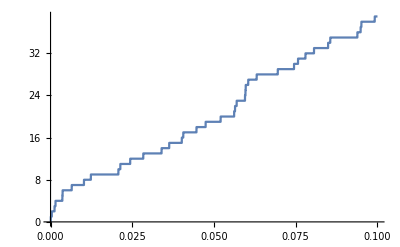

```mathematica
Plot[fall[[1,1]][Energy],{Energy,Emin,Emax},PlotPoints->100]
```

```mathematica
0.1/0.004/4
```

6.25

```mathematica
NERange[ΔE_,E0_,ic_,iens_]:=fall[[ic,iens]][E0+ΔE]-fall[[ic,iens]][E0]
```

```mathematica
Plot[NERange[ΔE,0.,1,1],{ΔE,Emin,Emax},PlotPoints->100]
```

InterpolatingFunction::dmval: Input value {1.01111×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
NumEns=100;
Emin=0.0;Emax=0.1;NumWindows=Table[(Emax-Emin)/SD[[ic,3]]/4,{ic,1,Length[SD]}]
```

{10.227,10.2249,10.1825,10.1313,10.0725,10.012,9.93167,9.86466,9.77746,9.70007,9.61612,9.52272,9.43824,9.37031,9.26818,9.18577,9.09719,9.01096,8.89363,8.79662,8.71202,8.59786,8.49041,8.38223,8.29958,8.19216,8.11688,8.02439,7.92845,7.84461,7.76639,7.6746,7.59624,7.4949,7.42567,7.34754,7.27336,7.18639,7.08577,6.98734,6.89636,6.82128,6.73056,6.65124,6.5767,6.50229,6.41947,6.33376,6.26975,6.20548}

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

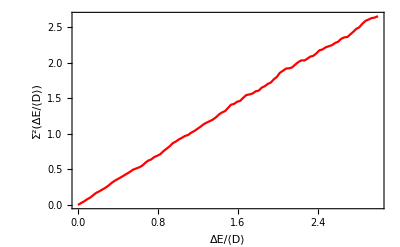

```mathematica
ΔEmax=(Emax-Emin)/13;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}];
nerange=Length[Erange]-1;
psigma2c1=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange))^2)/.DE->DEOverD SD[[ic,3]],
{ic,{1}}]],
{DEOverD,0,3},PlotPoints->50,MaxRecursion->1,
PlotStyle->{{Red},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨D⟩","Σ^2(ΔE/⟨D⟩)"}]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

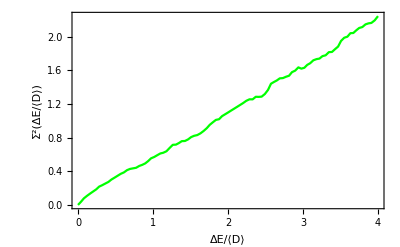

```mathematica
ΔEmax=(Emax-Emin)/7.;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}];
nerange=Length[Erange]-1;
psigma2cmid=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange))^2)/.DE->DEOverD SD[[ic,3]],
{ic,{9}}]],
{DEOverD,0,4},PlotPoints->50,MaxRecursion->1,
PlotStyle->{{Green},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨D⟩","Σ^2(ΔE/⟨D⟩)"}]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

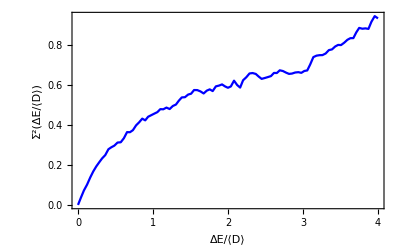

```mathematica
ΔEmax=(Emax-Emin)/6.;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}];
nerange=Length[Erange]-1;
psigma2cwigner=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange))^2)/.DE->DEOverD SD[[ic,3]],
{ic,{50}}]],
{DEOverD,0,4},PlotPoints->50,MaxRecursion->1,
PlotStyle->{{Blue},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨D⟩","Σ^2(ΔE/⟨D⟩)"}]
```

```mathematica
pSP=Plot[L/2+(1-Exp[-4 L])/8,{L,0,4},PlotStyle->{Black,Dotted}];
Sig2Formula[β_,r_]:=2/(β π^2)(Log[β π r]+EulerGamma+1-Cos[β π r]-CosIntegral[β π r]) + r(1-2/π SinIntegral[β π r]);
Sig2GOE[r_]:=2 Sig2Formula[2.0,r]+(SinIntegral[π r]/π)^2-1/π SinIntegral[π r];
psigendcases=Plot[{Sig2Formula[0.001,r],Sig2GOE[r]},{r,0,4},PlotStyle->{{Black,Dashed},{Black,Dashed}}];
```

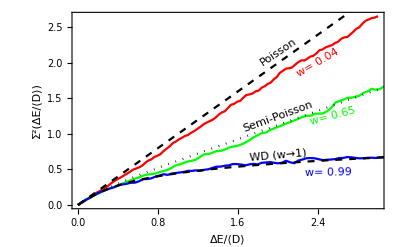

```mathematica
psig2=Show[psigma2c1,psigma2cmid,psigma2cwigner,pSP,psigendcases,
Epilog->{
Text[Style[Rotate["Poisson",34 Degree],Medium],{2.0,2.15}],
Text[Style[Rotate["Semi-Poisson",20 Degree],Medium],{2.0,1.25}],
Text[Style[Rotate["WD (w→1)",5 Degree],Medium],{2.0,0.7}],
Text[Style[Rotate[StringJoin["w= ",ToString[NumberForm[brodydata[[1,2]],{2,2}]]],30 Degree],{Medium,Red}],{2.4,2.0}],
Text[Style[Rotate[StringJoin["w= ",ToString[NumberForm[brodydata[[9,2]],{2,2}]]],15 Degree],{Medium,Green}],{2.55,1.25}],
Text[Style[Rotate[StringJoin["w= ",ToString[NumberForm[brodydata[[50,2]],{2,2}]]],1 Degree],{Medium,Blue}],{2.5,.45}]}]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/psigma2.pdf",psig2]
```

~/Code/Nchannel/Square/CODES/plots/psigma2.pdf

### What to expect for semi-poisson?

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0]
FitError[func_,list_,p_]:=Module[{tab1,nbin},
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}];
If[p==Null,
tab1=Table[(list[[i,2]]-func[list[[i,1]]])^2,{i,1,Length[list]}],
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}]
];
nbin=Length[tab1];
√(Total[tab1]/(nbin-1))
]
SemiPoisson[s_]:=4 s Exp[-2 s]
porterthomas[x_]:=Exp[-x/2]/(√(2π x))
genpt[x_,ν_]:=(ν/2 x)^(ν/2-1)/Gamma[ν/2] ν/2 Exp[-ν/2 x]
GenPTDistribution=ProbabilityDistribution[genpt[x,ν],{x,0,∞},Assumptions->ν>0]
```

ProbabilityDistribution[x^w ⅇ^(-(x Gamma[(2+w)/(1+w)])^(1+w)) (1+w) Gamma[(2+w)/(1+w)]^(1+w),{x,0,∞},Assumptions→w>0]

ProbabilityDistribution[(2^(-ν/2) ⅇ^(-(x ν)/2) ν (x ν)^(-1+ν/2))/Gamma[ν/2],{x,0,∞},Assumptions→ν>0]

If we sample the semi-poisson distribution, what Brody parameter do we expect, and with what standard error?

```mathematica
cumsp[s_]:=Integrate[4s Exp[-2s],{s,0,s}]
```

```mathematica
cumsp[s]
```

ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s)

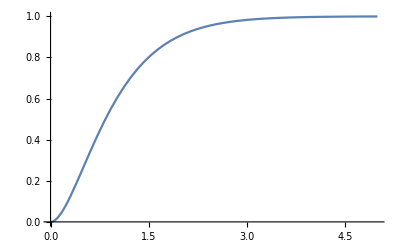

```mathematica
Plot[ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s),{s,0,5}]
```

```mathematica
spacing[u_]:=s/.FindRoot[u==ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s),{s,0.5},PrecisionGoal->20][[1]]
```

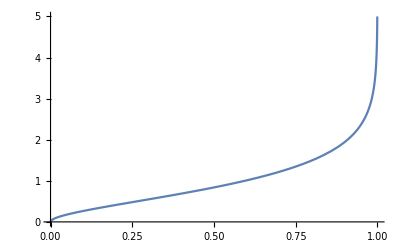

```mathematica
Plot[spacing[u],{u,0,1},PlotRange->{0,5}]
```

```mathematica
spacing[.9999]
```

5.87819

```mathematica
SPSample[n_]:=Module[{u,z},u=RandomReal[{0,0.9999999},n];Map[spacing,u]]
```

```mathematica
w0=0.74;
NP=1000;
dx=0.2;
Bins=Table[t,{t,0,5,dx}];
samp=SPSample[NP];
```

```mathematica
ChiSqr[func_,hist_,p_]:=Module[{tab1,nbin,dbin,Ntot},
dbin=hist[[2,1]]-hist[[1,1]];
Ntot=Total[hist[[All,2]]];
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]],p])^2/(Ntot dbin  func[hist[[i,1]],p]),{i,1,Length[hist]}];
Print[p];
If[p== Null,
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]]])^2/(Ntot dbin  func[hist[[i,1]]]),{i,1,Length[hist]}]
];
nbin=Length[hist];
Total[tab1]
]
```

```mathematica
Var[func_,P_]:=Module[{tab1,nbin,dbin,Ntot},
dbin=P[[2,1]]-P[[1,1]];
Ntot=Total[P[[All,2]]];
tab1=Table[0,{i,1,Length[P]}];
tab1=Table[(P[[i,2]]-func[P[[i,1]]])^2,{i,1,Length[P]}];

nbin=Length[P];
1/(nbin-1)Total[tab1]
]
```

```mathematica
bc=BinCounts[samp,{Bins}];
bcnorm=bc/NP/dx;
bnorm=Table[{(Bins[[i]]),bcnorm[[i]]},{i,1,Length[Bins]-1}];
bcfit=Table[{(Bins[[i]]+Bins[[i+1]])/2,bc[[i]]},{i,1,Length[Bins]-1}];
bfit=Table[{(Bins[[i]]+Bins[[i+1]])/2,bcnorm[[i]]},{i,1,Length[Bins]-1}];
```

```mathematica
ChiSqr[SemiPoisson,bcfit,Null]
```

Null

19.5923

```mathematica
ChiSqr[PBrody,bcfit,0.53]
```

0.53

45.1339

```mathematica
Var[SemiPoisson,bfit]
```

0.00106352

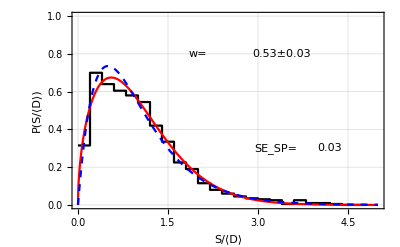

```mathematica
ph=ListPlot[bnorm,InterpolationOrder->0,Joined->True,PlotStyle->Black];
psp=Plot[4s Exp[-2s],{s,0,5},PlotStyle->{Blue,Dashed}];
nlm=NonlinearModelFit[bfit,{PBrody[z,w]},{{w,w0}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.9999];
pb=Plot[PBrody[z,w/.nlm["BestFitParameters"]],{z,0,5},PlotStyle->{Red}];
Show[{ph,pb,psp},PlotRange->{0,1},Frame->True,GridLines->Automatic,FrameLabel->{"S/⟨D⟩","P(S/⟨D⟩)"},LabelStyle->Large,Epilog->{
Text[Style["SE_SP= ",Large],{3.3,0.3}],
Text[Style["w=",Large],{2,0.8}],
Text[Style[NumberForm[FitError[SemiPoisson,bfit,Null],{2,2}],Large],{4.2,0.3}],Text[Style[NumberForm[w/.nlm["BestFitParameters"],{2,2}]±NumberForm[FitError[PBrody,bfit,w/.nlm["BestFitParameters"]],{2,2}],Large],{3.4,0.8}]}]
```

### Potential Alternatives to the Brody distribution

Are there other functions that extrapolate between the Poisson and Wigner limits?  The SP distribution appears to have the right idea, but doesn’t produce a χ^2≈1, so can we imagine another family of functions that achieves the desired goal but with less repulsion at intermediate values of w?

```mathematica
PBrody[s,w]
```

ⅇ^(-(s Gamma[(2+w)/(1+w)])^(1+w)) s^w (1+w) Gamma[(2+w)/(1+w)]^(1+w)

```mathematica
PBrody[s,0]
```

ⅇ^-s

```mathematica
PBrody[s,1]
```

1/2 ⅇ^(-(π s^2)/4) π s

```mathematica
SemiPoisson[s]
```

4 ⅇ^(-2 s) s

```mathematica
(Gamma[2+w]/Gamma[1+w])^(1+w)/.w->1
```

4

```mathematica
ⅇ^(-( Gamma[(2+w)/(1+w)])^(1+w)) /.w->1
```

ⅇ^(-π/4)

```mathematica
1/Integrate[ⅇ^(-(1+(π/4-1)w)s^(1+w)) s^w ,{s,0,∞},Assumptions->{w>0,w<1}]
```

1/4 (1+w) (4+(-4+π) w)

```mathematica
Integrate[((1+w) (4+(-4+π) w))/4 ⅇ^(-(1+(π/4-1)w)s^(1+w)) s^w,{s,0,∞},Assumptions->{w>0,w<1}]
```

1

```mathematica
PAlternative[s_,w_]:=((1+w) (4+(-4+π) w))/4 ⅇ^(-(1+(π/4-1)w)s^(1+w)) s^w
```

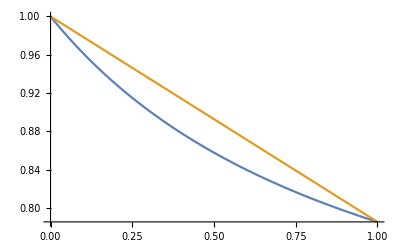

```mathematica
Plot[{(Gamma[(2+w)/(1+w)])^(1+w),1+(π/4-1)w},{w,0,1}]
```

```mathematica
AlternativeLSFit=Table[NonlinearModelFit[NewBrodyPDist[[ic]],PAlternative[z,w],{w},z,PrecisionGoal->0.001,Method->Automatic,ConfidenceLevel->0.9],{ic,1,50}];
```

```mathematica
AlternativeLSFit[[9]]["ParameterErrors"]
```

{0.0501891}

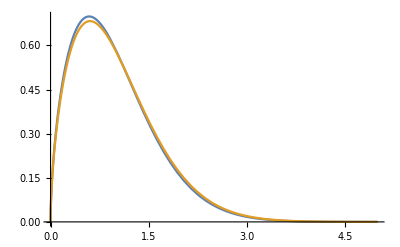

```mathematica
Plot[{PAlternative[s,.6],PBrody[s,.6]},{s,0,5}]
```